#### Change Point

Reference: 
“Handbook of Reliability Engineering Hoang Pham (Editor)” p.159

```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
N0=800;
n0=60;
λ10=3;
λ20=1;
τ0=30;
NN=Length[data];
INTERVAL=1;
```

```mathematica
data=Flatten[{Table[RandomVariate[ExponentialDistribution[λ10(N0-i+1)]],{i,1,τ0}],Table[RandomVariate[ExponentialDistribution[λ20(N0-j+1)]],{j,τ0+1,n0}]}];
```

```mathematica
τ0/Sum[(N0-i+1)data[[i]],{i,1,τ0}]
```

4.02865

```mathematica
(n0-τ0)/Sum[(N0-i+1)data[[i]],{i,τ0+1,n0}]
```

0.971704

```mathematica
PowerExpand[Log[1-Simplify[CDF[ExponentialDistribution[λ2],t],t≥0]]]
```

-t λ2

```mathematica
PowerExpand[Log[1-Simplify[CDF[ExponentialDistribution[λ1],t],t≥0]]]
```

-t λ1

```mathematica
U0[λ1_,λ2_,τ_,NN0_]:=(*-Sum[NN0-i+1,{i,1,Length[data]}]+*)Total[Table[t λ-Log[λ]/.{t->data[[i]],λ->λ1(NN0-i+1)},{i,1,τ}]]+Total[Table[t λ-Log[λ]/.{t->data[[i]],λ->λ2(NN0-i+1)},{i,τ+1,Length[data]}]](*-((NN0-τ) (-t λ1)/.t->Total[data[[1;;τ]]])-((NN0-Length[data]) (-t λ2)/.t->Total[data])*)
```

```mathematica
(*U[λ1_,λ2_,τ_]:=Total[Map[(# λ1-Log[λ1])&,data[[1;;τ]]]]+Total[Map[(# λ2-Log[λ2])&,data[[(τ+1);;Length[data]]]]]*)
```

```mathematica
U[λ1_,λ2_,τ_]:=U0[λ1,λ2,τ,N0]
```

```mathematica
U0[3,1,10,100]
```

-260.892

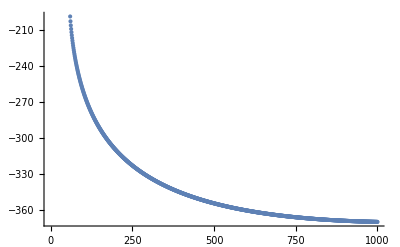

```mathematica
Table[U0[λ10,λ20,10,i],{i,1,1000}]//ListPlot
```

```mathematica
dU1[λ1_,λ2_,τ_]:=GradientG[U[λ1,λ2,τ],{λ1,λ2}]
```

```mathematica
ddU1[λ1_,λ2_,τ_]:=HessianH[U[λ1,λ2,τ],{λ1,λ2}]
```

```mathematica
dU[λ1_,λ2_,τ_]:=Apply[dU1,{x,y,τ}]/.{x->λ1,y->λ2}
```

```mathematica
ddU[λ1_,λ2_,τ_]:=Apply[ddU1,{x,y,τ}]/.{x->λ1,y->λ2}
```

```mathematica
ddU[1,2,10]
```

{{10.,0.},{0.,12.5}}

```mathematica
RandomVariate[DiscreteUniformDistribution[{1,10000}],5]
```

{4830,6491,3575,3252,925}

```mathematica
Dim=2;
BURNIN=2000;
EPISODE =6000;
CHAINS=3;
STEPS=3;
INTERVAL=101;
vanilla0= True;
switch=True;
diag=False;
switch0=200;
QS=List[];
QSN=List[];
QSτ=List[];
qinit=Table[1/Mean[data],CHAINS,Dim];
```

```mathematica
RandomVariate[DiscreteUniformDistribution[{1,Length[data]}],CHAINS]
```

{53,3,11}

```mathematica
CHAINS
```

3

```mathematica
decayenergy=DECAYENERGY;decaydt=DECAYDT;dt1=dt10;dt2=dt20;ND=NormalDistribution[];UD=UniformDistribution[];vanilla=vanilla0;ACS={};
qAll=qinit;
NAll=RandomVariate[DiscreteUniformDistribution[{1,100}],CHAINS];
τAll=RandomVariate[DiscreteUniformDistribution[{2,Length[data]-1}],CHAINS];
Utotal=Sum[Apply[ U,Flatten[{qAll[[i]],τAll[[i]]}]],{i,1,CHAINS}];
UUtotal=Utotal;
Htotal1=If[Utotal>0,2Utotal,100];
Htotal2=If[Utotal>0,2Utotal,100];
```

```mathematica
outbnd[q_]:=AnyTrue[q,(#≤0)&];
```

```mathematica
For[j=1,j⩽EPISODE,j++,
pAll=RandomVariate[ND,{CHAINS,Dim}];
KtotalNew = Sum[If[vanilla,pAll[[i]].pAll[[i]],pAll[[i]].If[diag,pAll[[i]]/Apply[ddU,Flatten[{qAll[[i]],τAll[[i]]}]],LinearSolve[Apply[ddU,Flatten[{qAll[[i]],τAll[[i]]}]],pAll[[i]],Method->"Krylov"]]]/2,{i,1,CHAINS}];
Utotal=Sum[Apply[ U,Flatten[{qAll[[i]],τAll[[i]]}]],{i,1,CHAINS}];
Htotal=If[vanilla,Htotal1,Htotal2];dt=If[vanilla,dt1,dt2];Ktotal=Htotal-Utotal;pAll=pAll Sqrt[Abs[Ktotal/KtotalNew]];AS={};ES={};
For[i=1,i<=CHAINS,i++,bad=False;p=pAll[[i]];q=qAll[[i]];q0=q;
If[j<=BURNIN,UE={Apply[U,Flatten[{q,τAll[[i]]}]]}];
For[step=1,step≤CHAINS,step++,
p=p-dt Apply[dU,Flatten[{q,τAll[[i]]}]];q1=q;
q=q+dt If[vanilla,p,If[diag,p/Apply[ddU,Flatten[{q,τAll[[i]]}]],LinearSolve[Apply[ddU,Flatten[{q,τAll[[i]]}]],p,Method->"Krylov"]]];
If[outbnd[q],bad=True;q=q1];
If[j<=BURNIN,UE=Append[UE,Apply[U,Flatten[{q,τAll[[i]]}]]]]];
If[j<=BURNIN,ES=Append[ES,UE]];
α=If[bad,0,Exp[Clip[Apply[U,Flatten[{q0,τAll[[i]]}]]-Apply[U,Flatten[{q,τAll[[i]]}]],{-20,0}]]];
AS=Append[AS,N[α]];
If[bad || α<RandomVariate[UD],q=q0];
qAll[[i]]=q;
If[j>BURNIN,QS=Append[QS,q]]];

If[Mod[j,INTERVAL]==0,Print[Row[{j,Ktotal,KtotalNew,Mean[AS],StandardDeviation[AS],Utotal,Htotal1,Htotal2,dt1,dt2,vanilla,s,S},"     "]]];
If[j<=BURNIN,
s=Union[Flatten[Table[Ordering[ES[[i]],1],{i,1,CHAINS}]]];
S=Union[Flatten[Table[Ordering[ES[[i]],-1],{i,1,CHAINS}]]];
If[s=={1,STEPS+1}&&S=={1,STEPS+1},dt=dt (1+decaydt)];
If[s=={1}&&S=={STEPS+1},dt=dt/(1+decaydt)]];
If[j<=BURNIN&&Ktotal>0,
hi=Mean[AS]>HIGHAP;
lo=Mean[AS]<LOWAP;
If[hi,Htotal=(Htotal-Utotal)(1+decayenergy)+Utotal,If[lo,Htotal=(Htotal-Utotal)/(1+decayenergy)+Utotal]]];
(*If[Htotal<Utotal&&Htotal>0,If[hi,Htotal=Htotal/(1+decayenergy)-1,If[lo,Htotal=1+Htotal(1+decayenergy)]]];
If[Utotal<Htotal&&Htotal>0,If[hi,Htotal=(1+decayenergy)Htotal+1,If[lo,Htotal=Htotal/(1+decayenergy)-1]]];
If[Htotal<Utotal&&Htotal<0,If[hi,Htotal=Htotal(1+decayenergy)-1,If[lo,Htotal=Htotal/(1+decayenergy)+1]]];
If[Utotal<Htotal&&Htotal<0,If[hi,Htotal=Htotal/(1+decayenergy)+1,If[lo,Htotal=Htotal(1+decayenergy)-1]]]];*)

If[vanilla,Htotal1=Htotal;dt1=dt,Htotal2=Htotal;dt2=dt];
If[switch&&j>switch0,vanilla=Not[vanilla]];
For[i=1,i<=CHAINS,i++,
τ0=τAll[[i]];
τ1=RandomVariate[DiscreteUniformDistribution[{2,Length[data]-1}]];
(*τ1=τ0+RandomChoice[{-1,1}];*)
If[τ1==1||τ1==Length[data],α=0,α=Exp[Clip[Apply[U,Flatten[{qAll[[i]],τ0}]]-Apply[U,Flatten[{qAll[[i]],τ1}]],{-20,0}]]];
If[α>=RandomVariate[UD],τAll[[i]]=τ1];
If[j>BURNIN,QSτ=Append[QSτ,τAll[[i]]]];
]
];
```

1012.30679×10^73.913920.3333330.57735133849.2.32018×10^7268426.0.00005933491.×10^-7True{1,4}{1,4}

202235577.7.8146×10^60.9240460.11535232849.12.55124×10^7268426.0.0164241.×10^-7False{1,4}{1,4}

303825794.4.477571.3741×10^-91.19001×10^-9853.939826648.1.91057×10^60.006965373.74043×10^-6True{1,4}{1,4}

4042.79763×10^68859.090.3595420.556044-949.006111644.2.79668×10^60.001378060.000186218False{1,2}{4}

50552635.2.066670.7363310.456689-1137.1451497.93.07646×10^60.000777880.000329897True{1,2}{4}

6063.07759×10^61.104650.5478940.439963-1134.3942363.13.07645×10^60.0009412340.000329897False{1}{4}

70732678.23.730310.6381210.393081-1132.3731545.92.79667×10^60.001515870.000531302True{1,3,4}{1,4}

8082.79781×10^60.2639820.1581940.128872-1132.0928574.82.79667×10^60.001252780.000483002False{1,2}{4}

90932682.13.396660.4983730.409401-1137.31545.12.54233×10^60.001252780.000439093True{1,2}{4}

10102.10203×10^61.217910.7458620.232698-1134.2228574.72.1009×10^60.001252780.000483002False{1,2}{4}

111120287.4.724740.09550320.127896-1130.3319156.62.1009×10^60.001515870.000329897True{1}{4}

12122.79781×10^60.5820250.4685460.47805-1135.3725872.92.79667×10^60.0005844320.000584432False{1,3,4}{1,4}

131332679.12.38271.0.-1134.4631544.62.1009×10^60.0007071630.000483002True{1,3}{1,4}

14142.31223×10^60.2814850.4047810.525335-1131.3751493.52.3111×10^60.000777880.000483002False{1,2}{4}

151552623.2.500620.4697220.46431-1130.0851492.92.3111×10^60.0007071630.000584432True{1,3,4}{1,4}

16162.10203×10^60.636550.2862480.428535-1129.8334812.42.1009×10^60.001378060.000439093False{1}{4}

171729709.92.054450.5153690.251298-1136.1328573.82.54233×10^60.001035360.000272642True{1,2,4}{1,4}

18182.79781×10^60.8425670.6081950.477092-1134.8728574.2.79667×10^60.001138890.000329897False{1}{4}

191929711.51.812220.3695840.54828-1137.6428573.93.72275×10^60.0009412340.000362887True{1}{4}

20203.38535×10^62.589450.7734060.246051-1135.51496.13.38421×10^60.0009412340.000362887False{1,2}{4}

212152632.83.878520.6450040.420509-1136.6951496.13.38421×10^60.0009412340.000362887True{1,2}{4}

22223.38535×10^60.6299960.7954020.354374-1136.51496.13.38421×10^60.0009412340.000362887False{1,2}{4}

232352629.93.063940.3216850.384834-1133.8551496.13.38421×10^60.0009412340.000362887True{1,2}{4}

24243.38535×10^60.1971530.235690.264377-1134.451496.13.38421×10^60.0009412340.000362887False{1,2}{4}

252552632.10.8550910.4913760.49945-1136.0751496.13.38421×10^60.0009412340.000362887True{1,2}{4}

26263.38535×10^60.2261010.7223440.359976-1132.9451496.13.38421×10^60.0009412340.000362887False{1,2}{4}

272752630.71.115390.3868160.53703-1134.6551496.13.38421×10^60.0009412340.000362887True{1,2}{4}

28283.38535×10^60.6054990.1462130.109362-1132.1851496.13.38421×10^60.0009412340.000362887False{1,2}{4}

292952631.0.3722040.3086150.43302-1134.9351496.13.38421×10^60.0009412340.000362887True{1,2}{4}

30303.38535×10^60.207520.2182880.19073-1131.1951496.13.38421×10^60.0009412340.000362887False{1,2}{4}

313152628.82.181030.2026140.322298-1132.7351496.13.38421×10^60.0009412340.000362887True{1,2}{4}

32323.38535×10^60.5565430.677460.422077-1136.1251496.13.38421×10^60.0009412340.000362887False{1,2}{4}

333352624.92.59860.5697510.505521-1128.851496.13.38421×10^60.0009412340.000362887True{1,2}{4}

34343.38535×10^60.6079120.3485330.290977-1134.3651496.13.38421×10^60.0009412340.000362887False{1,2}{4}

353552632.44.021840.0003542220.000326582-1136.3751496.13.38421×10^60.0009412340.000362887True{1,2}{4}

36363.38535×10^60.8714430.3059930.288697-1131.4351496.13.38421×10^60.0009412340.000362887False{1,2}{4}

373752632.61.666940.6191110.537944-1136.4951496.13.38421×10^60.0009412340.000362887True{1,2}{4}

38383.38535×10^60.1397210.6876110.541073-1132.5651496.13.38421×10^60.0009412340.000362887False{1,2}{4}

393952631.23.036740.1766990.0717597-1135.1651496.13.38421×10^60.0009412340.000362887True{1,2}{4}

40403.38534×10^60.05653920.4114890.510658-1129.4851496.13.38421×10^60.0009412340.000362887False{1,2}{4}

414152627.95.026770.3454810.567051-1131.7951496.13.38421×10^60.0009412340.000362887True{1,2}{4}

42423.38535×10^61.609940.7006990.518404-1135.3951496.13.38421×10^60.0009412340.000362887False{1,2}{4}

434352624.44.161360.3852370.537236-1128.3651496.13.38421×10^60.0009412340.000362887True{1,2}{4}

44443.38535×10^60.7098950.3254920.272222-1135.8151496.13.38421×10^60.0009412340.000362887False{1,2}{4}

454552627.31.953540.2570850.318834-1131.1951496.13.38421×10^60.0009412340.000362887True{1,2}{4}

46463.38535×10^60.53620.2885370.246371-1132.8851496.13.38421×10^60.0009412340.000362887False{1,2}{4}

474752626.54.560231.0.-1130.4551496.13.38421×10^60.0009412340.000362887True{1,2}{4}

48483.38535×10^60.1132470.6178290.485983-1132.9251496.13.38421×10^60.0009412340.000362887False{1,2}{4}

494952629.22.555220.6667930.577131-1133.1651496.13.38421×10^60.0009412340.000362887True{1,2}{4}

50503.38535×10^61.998190.2985180.38674-1136.2151496.13.38421×10^60.0009412340.000362887False{1,2}{4}

515152631.75.977290.4395940.510664-1135.6251496.13.38421×10^60.0009412340.000362887True{1,2}{4}

52523.38535×10^60.6538180.1685560.0678986-1137.7251496.13.38421×10^60.0009412340.000362887False{1,2}{4}

535352628.63.04920.2011290.183194-1132.5151496.13.38421×10^60.0009412340.000362887True{1,2}{4}

54543.38535×10^61.289230.6243040.329757-1131.3751496.13.38421×10^60.0009412340.000362887False{1,2}{4}

555552627.92.604640.5718270.515245-1131.8151496.13.38421×10^60.0009412340.000362887True{1,2}{4}

56563.38535×10^60.4401390.2389490.189348-1135.6751496.13.38421×10^60.0009412340.000362887False{1,2}{4}

575752632.61.944170.3555190.317096-1136.5551496.13.38421×10^60.0009412340.000362887True{1,2}{4}

58583.38535×10^60.6078840.1283150.217296-1131.3851496.13.38421×10^60.0009412340.000362887False{1,2}{4}

595952626.42.011510.1474980.209687-1130.3251496.13.38421×10^60.0009412340.000362887True{1,2}{4}

```mathematica
Median[QS]
```

{3.79251,0.998853}

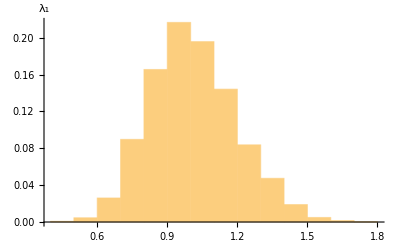

```mathematica
Histogram[QS[[;;,2]],Automatic,"Probability",AxesLabel->"λ_1"]
```

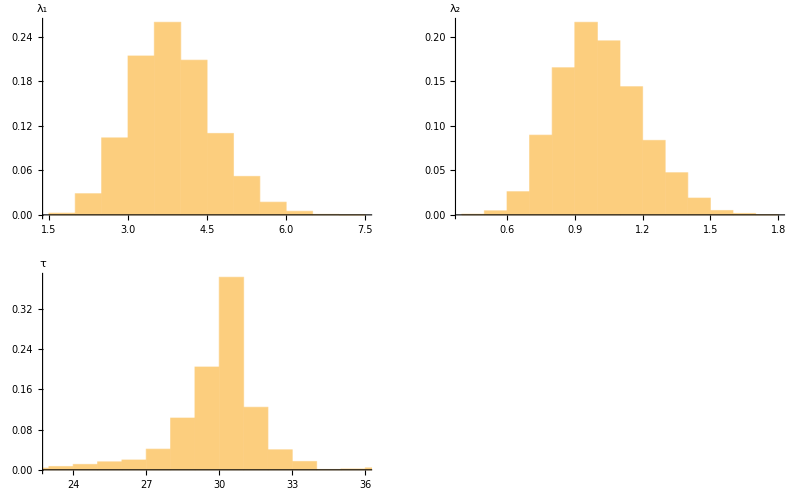

```mathematica
GraphicsGrid[{{Histogram[QS[[;;,1]],Automatic,"Probability",AxesLabel->"λ_1"],Histogram[QS[[;;,2]],Automatic,"Probability",AxesLabel->"λ_2"]},{Histogram[QSτ,Automatic,"Probability",AxesLabel->"τ"]}}]
```

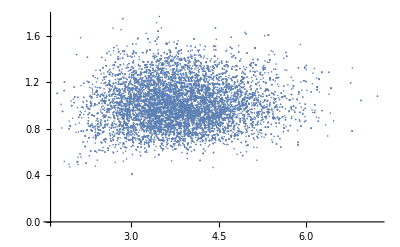

```mathematica
ListPlot[QS]
```

```mathematica
Quantile[QS,{.025,.975}]//MatrixForm
```

(2.42742 | 5.47163
0.687322 | 1.40087)

```mathematica
Mean[QS]
```

{3.83755,1.01084}

```mathematica
Map
```

Map

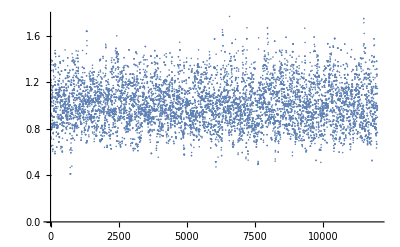

```mathematica
ListPlot[QS[[;;,2]]]
```

```mathematica
QS//Transpose//Dimensions
```

{2,12000}

```mathematica
QSτ//Dimensions
```

{12000}

```mathematica
QQ={QS[[;;,1]],QS[[;;,2]],QSτ}//Transpose;
```

```mathematica
QQ
```

{{4.43923,1.34952,30},{5.07116,1.07666,30},{3.99327,1.00612,30},{4.43923,1.34952,31},{4.27847,1.14248,30},{2.77019,1.01332,30},{4.43923,1.34952,31},{4.45724,1.03609,30},{3.4004,0.811802,30},11983,{5.42925,1.10135,30},{3.37809,0.99487,30},{3.03885,0.970325,30},{4.91064,0.767933,30},{3.37809,0.99487,30},{2.60754,0.899201,30},{4.91064,0.767933,30},{2.71282,1.14561,30}}
 |  |  |  |

```mathematica
Take
```

Take

```mathematica
ListPointPlot3D[QQ,AxesLabel->{Subscript[λ, 1],Subscript[λ, 2],τ},PlotLabel->"Point cloud"]
```

-Graphics3D-

```mathematica
TakeWhile[QQ,Take[#,3]>2&]
```

{}

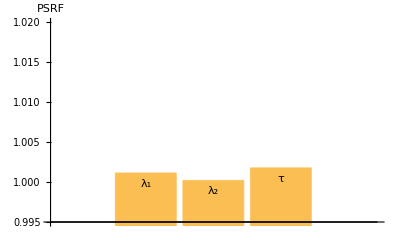

```mathematica
BarChart[psrf[{QS[[;;,1]],QS[[;;,2]],QSτ}//Transpose],PlotRange->{Automatic,{.995,1.02}},AxesLabel->"PSRF",ChartLabels->Placed[{"λ_1","λ_2","τ"},Top]]
```

```mathematica
psrf[QS]
```

{1.00114,1.00021}

```mathematica
psrf[{QSτ}//Transpose]//N
```

{1.00178}

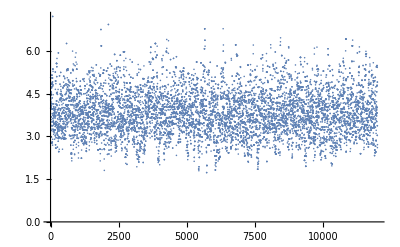

```mathematica
ListPlot[QS[[;;,1]]]
```

```mathematica
(*Export["jelinski-moranda.csv",QS]*)
```

```mathematica
Length[QSτ]
```

12000

```mathematica
U1[θ1_,θ2_]=U[θ1,θ2,τ0]
```

7.44667 θ1+30.8736 θ2-Log[771 θ1]-Log[772 θ1]-Log[773 θ1]-Log[774 θ1]-Log[775 θ1]-Log[776 θ1]-Log[777 θ1]-Log[778 θ1]-Log[779 θ1]-Log[780 θ1]-Log[781 θ1]-Log[782 θ1]-Log[783 θ1]-Log[784 θ1]-Log[785 θ1]-Log[786 θ1]-Log[787 θ1]-Log[788 θ1]-Log[789 θ1]-Log[790 θ1]-Log[791 θ1]-Log[792 θ1]-Log[793 θ1]-Log[794 θ1]-Log[795 θ1]-Log[796 θ1]-Log[797 θ1]-Log[798 θ1]-Log[799 θ1]-Log[800 θ1]-Log[741 θ2]-Log[742 θ2]-Log[743 θ2]-Log[744 θ2]-Log[745 θ2]-Log[746 θ2]-Log[747 θ2]-Log[748 θ2]-Log[749 θ2]-Log[750 θ2]-Log[751 θ2]-Log[752 θ2]-Log[753 θ2]-Log[754 θ2]-Log[755 θ2]-Log[756 θ2]-Log[757 θ2]-Log[758 θ2]-Log[759 θ2]-Log[760 θ2]-Log[761 θ2]-Log[762 θ2]-Log[763 θ2]-Log[764 θ2]-Log[765 θ2]-Log[766 θ2]-Log[767 θ2]-Log[768 θ2]-Log[769 θ2]-Log[770 θ2]

```mathematica
U2[t_]:=U[7.185379241533938,1.1871557257653718,t]
```

```mathematica
|
```

```mathematica
mle=FindMinimum[{U0[x,y,τ0,N0],x>0&&y>0},{x,y}]
```

{-379.749,{x→4.02865,y→0.971704}}

```mathematica
Sqrt[1/ddU[x,y,30]]/.Last[mle]
```

Power::infy: Infinite expression 1/0. encountered.

{{0.735527,ComplexInfinity},{ComplexInfinity,0.177408}}

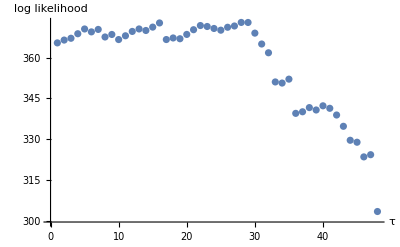

```mathematica
ListPlot[Table[-U2[i],{i,2,49}],AxesLabel->{"τ","log likelihood"}]
```

```mathematica
U[λ1_,λ2_]:=U0[λ1,λ2,τ0,N0]
```

```mathematica
ddU1[λ1_,λ2_]:=HessianH[U[λ1,λ2],{λ1,λ2}]
```

```mathematica
ddU[λ1_,λ2_]:=Apply[ddU1,{x,y}]/.{x->λ1,y->λ2}
```

```mathematica
ddU[1,1]
```

{{30.,0.},{0.,30.}}

```mathematica
sd=Sqrt[1/Diagonal[ddU[x,y]]/.Last[mle]]
```

{0.735527,0.177408}

```mathematica
Last[mle][[1]]
```

x→4.02865

```mathematica
MatrixForm[{{x Exp[-InverseCDF[NormalDistribution[],.975] sd[[1]]/x]/.Last[mle],x/.Last[mle][[1]],x Exp[InverseCDF[NormalDistribution[],.975] sd[[1]]/x]/.Last[mle]},{y Exp[-InverseCDF[NormalDistribution[],.975] sd[[2]]/y]/.Last[mle],y/.Last[mle][[2]],y Exp[InverseCDF[NormalDistribution[],.975] sd[[2]]/y]/.Last[mle]}}]
```

(2.81677 | 4.02865 | 5.76191
0.679402 | 0.971704 | 1.38977)

```mathematica
Quantile[QS,{.025,.5,.975}]//MatrixForm
```

(2.42742 | 3.79234 | 5.47163
0.687322 | 0.998853 | 1.40087)